```mathematica
ClearAll["Global`*"]
getconstraints[ntriag_]:={
constraints1 =Table[
(Symbol["x"<>ToString[n]] - Symbol["x"<>ToString[n+1]])^2 +
 (Symbol["y"<>ToString[n]] - Symbol["y"<>ToString[n+1]])^2 == (Symbol["d"<>ToString[n]])^2
,{n,ntriag}
];
constraints2 =Table[
(Symbol["x"<>ToString[n]] - Symbol["x"<>ToString[n+2]])^2 +
 (Symbol["y"<>ToString[n]] - Symbol["y"<>ToString[n+2]])^2 == (Symbol["h"<>ToString[n]])^2
,{n,ntriag}
];
Join[constraints1,constraints2](*= Join[constraints1,constraints2]*)
}

ntriag =4
symbols = Transpose@Table[{Symbol["x"<>ToString[n]] ,Symbol["y"<>ToString[n]],Symbol["h"<>ToString[n]],Symbol["d"<>ToString[n]]},{n,ntriag}];

x = symbols[[1,All]];
y = symbols[[2,All]];
h = symbols[[3,All]];
d = symbols[[4,All]];

cons = getconstraints[ntriag];
cons = cons[[1]];
(*
x1 =0;
y1 = 0;
x2 =1;
y2 =0;
x5 = 0;
y5 = 2;

d1 =1;
d2 =1;
d3 = 1;
d4 = 1;
h1 = 1;
h2 = 1.1;
h3 = 1;
h4 = 1;
*)
cons//Column
```

4

(x1-x2)^2+(y1-y2)^2==d1^2
(x2-x3)^2+(y2-y3)^2==d2^2
(x3-x4)^2+(y3-y4)^2==d3^2
(x4-x5)^2+(y4-y5)^2==d4^2
(x1-x3)^2+(y1-y3)^2==h1^2
(x2-x4)^2+(y2-y4)^2==h2^2
(x3-x5)^2+(y3-y5)^2==h3^2
(x4-x6)^2+(y4-y6)^2==h4^2

```mathematica
sols = NSolve[cons]
sol1=sols[[1]]
```

$Aborted

{1==d1^2,(1-x3)^2+y3^2==d2^2,(x3-x4)^2+(y3-y4)^2==d3^2,x4^2+(-2+y4)^2==d4^2,x3^2+y3^2==h1^2,(1-x4)^2+y4^2==h2^2,x3^2+(-2+y3)^2==h3^2,(x4-x6)^2+(y4-y6)^2==h4^2}

```mathematica
MeshRegion[{
{x1,y1},
{x2,y2},
{Values[sol1[[1]]],Values[sol1[[4]]]},
{Values[sol1[[2]]],Values[sol1[[5]]]},
{Values[sol1[[3]]],Values[sol1[[6]]]}
},
{Line[{1,2}],
Line[{2,3}],
Line[{3,4}],
Line[{4,5}],
Line[{1,3}],
Line[{2,4}],
Line[{3,5}]}]
```

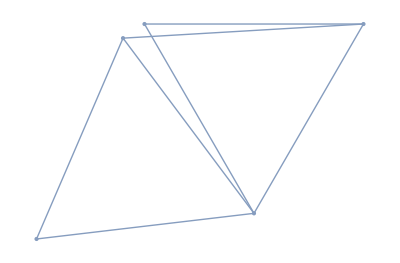

```mathematica
Values[sol1[[1]]]
```

1/2

```mathematica
{{0,0}
```

```mathematica
{{a1,b1,c1,d1,e1},{a2,b2,c2,d2,e2}}
```